## Generate and Solve Master Equation

simples example with two level system, but the procedure is general and will work for any size hamiltonian

```mathematica
(*build hamiltonian and symbolic ρ*)
Clear[ρ]
Clear[Ω,Δ];
H = ({{0, Ω}, {Ω, -Δ}});
dim = Length[H];
Ω = 1; Δ =0.1;
ρ0={{1,0},{0,0}};
rho=Array[ρ[#1,#2][t]&,{dim,dim}];
(*enforce conjugate relationship of ρ's off-diagonals *)
eqIdcs = {};
For[i=1,i<dim+1,i++,
For[j=dim,j>i,j--,
rho[[j,i]] = Conjugate[rho[[i,j]]];
AppendTo[eqIdcs,{i,j}]
]
];
(*generate non-redundant eqs and initial conditions*)
comm = rho.H - H.rho;
rhoPruned ={};
eqsPruned = {};
rhoICPruned = {};
For[i=1,i<dim+1,i++,
For[j=1,j<dim+1,j++,
If[i<=j,
AppendTo[eqsPruned,D[rho[[i,j]],t]==ⅈ comm[[i,j]]];
AppendTo[rhoICPruned,(rho/.t-> 0)[[i,j]]==ρ0[[i,j]]];
AppendTo[rhoPruned,rho[[i,j]]]
]
]
]
(*generate indices for population and coherence terms in pruned eq list*)
popIdxList ={1};
cohIdxList = {};
j=0;
last = 1;
elems = dim(dim+1)/2;
For[i=1,i<elems,i++
If[i ==last+dim-j,
{AppendTo[popIdxList,i],last=i,j++},
AppendTo[cohIdxList,i]
]
]
```

```mathematica
res= Timing[NDSolve[Flatten@Join[eqsPruned,rhoICPruned], rhoPruned, {t,0,2π*100}]];
Print["Time to run sim: ",res[[1]]];
s = res[[2]];
```

Time to run sim: 0.046875

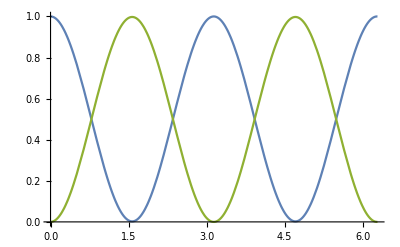

```mathematica
plt ={};
For[i=1, i<Length[s[[1]]]+1,i++,
plt = Append[plt,s[[1]][[i]][[2]]]
];
Plot[plt, {t, 0, 2π}]
```

## Same 2 level Hamiltonian, but now put it in Louiville space

```mathematica
Clear[ρ,n,j,m,k, eqs]
H = ({{0, Ω}, {Ω, -Δ}});
Ω = 1; Δ =10;
```

The von Neumann eq in Louiville space reads ℏ D[ρ,t] = - ⅈ L ρ. The L element corresponding to the ρmn equation is:

```mathematica
dim = (Dimensions[H][[1]])^2
Lnm[n,m,j,k]=Sum[H[[n,j]]KroneckerDelta[m,k]-H[[k,m]]KroneckerDelta[j,n],{j,1,dim},{k,1,dim}]; (*this would take some more work to actually build the matrix from this element*)
```

4

Part::pkspec1: The expression n cannot be used as a part specification.

Part::pkspec1: The expression m cannot be used as a part specification.

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

For a two level Hamiltonian, L is

```mathematica
L = ({{0, 0, -H[[2,1]], H[[1,2]]}, {0, 0, H[[2,1]], -H[[1,2]]}, {-H[[1,2]], H[[1,2]], H[[1,1]]-H[[2,2]], 0}, {H[[2,1]], -H[[2,1]], 0, H[[2,2]]-H[[1,1]]}})
```

{{0,0,-1,1},{0,0,1,-1},{-1,1,10,0},{1,-1,0,-10}}

```mathematica
ρvec = Array[ρ[#1][t] &,4];
ρvec[[4]] =Conjugate[ρvec[[2]]]
```

Conjugate[ρ[2][t]]

```mathematica
RHS = -ⅈ L.ρvec
```

{-ⅈ (Conjugate[ρ[2][t]]-ρ[3][t]),-ⅈ (-Conjugate[ρ[2][t]]+ρ[3][t]),-ⅈ (-ρ[1][t]+ρ[2][t]+10 ρ[3][t]),-ⅈ (-10 Conjugate[ρ[2][t]]+ρ[1][t]-ρ[2][t])}

Prune the eqs:

```mathematica
RHSpruned = {-ⅈ (Conjugate[ρ[2][t]]-ρ[3][t]),-ⅈ (-Conjugate[ρ[2][t]]+ρ[3][t]),-ⅈ (-10 Conjugate[ρ[2][t]]+ρ[1][t]-ρ[2][t])};
ρpruned = {ρ[1][t],ρ[2][t],ρ[3][t]};
```

```mathematica
ρvec[[1]]
```

ρ[1][t]

```mathematica
ρ0= {1,0,0};
```

```mathematica
eqs = Flatten@Join[{D[ρpruned,t] == RHSpruned, ρpruned ==ρ0/.t->0}]
```

{{ρ[1]'[t],ρ[2]'[t],ρ[3]'[t]}=={-ⅈ (Conjugate[ρ[2][t]]-ρ[3][t]),-ⅈ (-Conjugate[ρ[2][t]]+ρ[3][t]),-ⅈ (-10 Conjugate[ρ[2][t]]+ρ[1][t]-ρ[2][t])},{ρ[1][0],ρ[2][0],ρ[3][0]}=={1,0,0}}

```mathematica
res= Timing[NDSolve[eqs, ρpruned, {t,0,2π*100}]]
Print["Time to run sim: ",res[[1]]];
```

{1.98438,{{ρ[1][t]→InterpolatingFunction[{{0., 628.319}}, <>][t],ρ[2][t]→InterpolatingFunction[{{0., 628.319}}, <>][t],ρ[3][t]→InterpolatingFunction[{{0., 628.319}}, <>][t]}}}

Time to run sim: 1.98438

```mathematica
s = res[[2]];
plt ={};
For[i=1, i<Length[s[[1]]]+1,i++,
plt = Append[plt,s[[1]][[i]][[2]]]
];
Plot[plt, {t, 0, 2π}]
```

-Graphics-